# Multistage Graphs

## Definition of a Multistage Graph

The following code draws a multistage graph of 5 stages:

```mathematica
m=({{∞, 9, 7, 3, 2, ∞, ∞, ∞, ∞, ∞, ∞, ∞}, {∞, ∞, ∞, ∞, ∞, 4, 2, 1, ∞, ∞, ∞, ∞}, {∞, ∞, ∞, ∞, ∞, 2, 7, ∞, ∞, ∞, ∞, ∞}, {∞, ∞, ∞, ∞, ∞, ∞, ∞, 11, ∞, ∞, ∞, ∞}, {∞, ∞, ∞, ∞, ∞, ∞, 11, 8, ∞, ∞, ∞, ∞}, {∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, 6, 5, ∞, ∞}, {∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, 4, 3, ∞, ∞}, {∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, 5, 6, ∞}, {∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, 4}, {∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, 2}, {∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, 5}, {∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞}});
```

```mathematica
t=Flatten[DeleteCases[Table[If[m[[i,j]]==Infinity,Null,{i->j, m[[i,j]]}],{i,1,12},{j,1,12}],Null,2],1];
```

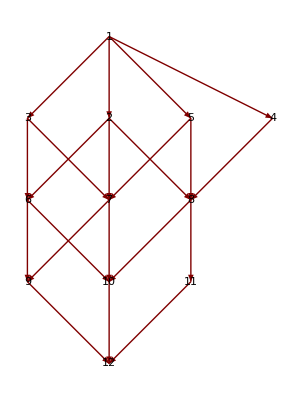

```mathematica
LayeredGraphPlot[t, VertexLabeling->True, EdgeLabeling->True]
```

## Resource Allocation Problem

Forward approach

Backward approach

```mathematica
V={{1},{2,3,4,5},{6,7,8},{9,10,11},{12}};
```

```mathematica
cost[i_,j_]:=Min[Table[If[i+1==Length[V],m[[j,l]],m[[j,l]]+cost[i+1,l]],{l,V[[i+1]]}]];
```

```mathematica
cost[1,1]
```

16